### Calculating v0 average and ω average in Non-Rotating Reference Frame ( To Compare to ω calculated in Rotating, and to supply initial guess values to rotating reference frame nonlinear model fitting)

```mathematica
ClearAll["Global`*"]
```

Call in data from tracker.

```mathematica
IRFraw=Import[FileNames["IRF_puck_x_y.csv",NotebookDirectory[],2][[1]]]
```

{{0,4.56,6.894},{0.017,4.879,5.091},{0.033,5.091,3.076},{0.05,5.091,1.061},{0.1,5.091,-6.257},{0.117,5.091,-8.591},{0.133,5.409,-10.818},{0.15,5.303,-13.151},{0.167,5.409,-14.954},{0.183,5.409,-17.075},{0.2,5.515,-19.408},{0.217,5.727,-21.211},{0.233,6.045,-23.014},{0.25,6.045,-25.135},{0.267,6.363,-27.15},{0.283,6.363,-28.741},{0.3,6.682,-30.969},{0.317,6.682,-32.771},{0.333,7.106,-34.574},{0.35,7.318,-36.483},{0.367,7.212,-38.286},{0.383,7.954,-39.877},{0.4,8.166,-41.68},{0.417,8.485,-43.377},{0.433,8.803,-45.18},{0.45,9.651,-47.089},{0.467,9.757,-48.892},{0.483,9.969,-50.801}}

```mathematica
t1=IRFraw[[3,1]]
```

0.033

```mathematica
t2=IRFraw[[Length[IRFraw]-2,1]]
```

0.45

```mathematica
IRFx={#[[1]],#[[2]]}&/@IRFraw
```

{{0,4.56},{0.017,4.879},{0.033,5.091},{0.05,5.091},{0.1,5.091},{0.117,5.091},{0.133,5.409},{0.15,5.303},{0.167,5.409},{0.183,5.409},{0.2,5.515},{0.217,5.727},{0.233,6.045},{0.25,6.045},{0.267,6.363},{0.283,6.363},{0.3,6.682},{0.317,6.682},{0.333,7.106},{0.35,7.318},{0.367,7.212},{0.383,7.954},{0.4,8.166},{0.417,8.485},{0.433,8.803},{0.45,9.651},{0.467,9.757},{0.483,9.969}}

```mathematica
IRFy={#[[1]],#[[3]]}&/@IRFraw
```

{{0,6.894},{0.017,5.091},{0.033,3.076},{0.05,1.061},{0.1,-6.257},{0.117,-8.591},{0.133,-10.818},{0.15,-13.151},{0.167,-14.954},{0.183,-17.075},{0.2,-19.408},{0.217,-21.211},{0.233,-23.014},{0.25,-25.135},{0.267,-27.15},{0.283,-28.741},{0.3,-30.969},{0.317,-32.771},{0.333,-34.574},{0.35,-36.483},{0.367,-38.286},{0.383,-39.877},{0.4,-41.68},{0.417,-43.377},{0.433,-45.18},{0.45,-47.089},{0.467,-48.892},{0.483,-50.801}}

```mathematica
x[t_]=Interpolation[IRFx][t]
```

InterpolatingFunction[…][t]

```mathematica
y[t_]=Interpolation[IRFy][t]
```

InterpolatingFunction[…][t]

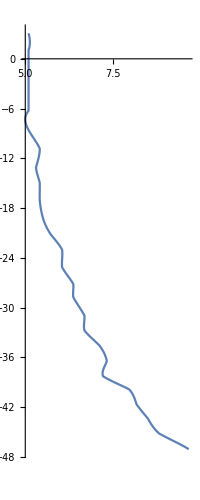

```mathematica
ParametricPlot[{x[t],y[t]},{t,t1,t2}]
```

```mathematica
dx[t_]=D[x[t],t]
```

InterpolatingFunction[…][t]

```mathematica
dy[t_]=D[y[t],t]
```

InterpolatingFunction[…][t]

```mathematica
ds[t_]=√(dx[t]^2+dy[t]^2)
```

√((InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^2)

```mathematica
v0ave=1/(t2-t1)NIntegrate[ds[t],{t,t1,t2}]
```

121.788

```mathematica
v0ave//Framed(*cm/s*)
```

121.788

## Calculating ω average from the position of the tape on table

```mathematica
ωraw=Import[FileNames["IRF_tape_x_y.csv",NotebookDirectory[],2][[1]]]
```

{{0,-41.786,-18.666},{0.017,-40.882,-20.534},{0.033,-39.861,-22.326},{0.05,-38.859,-24.127},{0.067,-37.672,-25.823},{0.083,-36.454,-27.528},{0.1,-35.112,-29.108},{0.117,-33.745,-30.724},{0.133,-32.242,-32.231},{0.15,-30.669,-33.681},{0.167,-29.05,-35.014},{0.183,-27.413,-36.295},{0.2,-25.669,-37.554},{0.217,-23.891,-38.657},{0.233,-22.051,-39.734},{0.25,-20.177,-40.729},{0.267,-18.237,-41.596},{0.283,-16.223,-42.397},{0.3,-14.179,-43.045},{0.317,-12.16,-43.69},{0.333,-10.079,-44.208},{0.35,-7.957,-44.602},{0.367,-5.828,-44.906},{0.383,-3.709,-45.015},{0.4,-1.573,-45.116},{0.417,0.52,-45.124},{0.433,2.627,-44.996},{0.45,4.417,-44.567},{0.467,6.739,-44.112},{0.483,8.74,-44.083}}

```mathematica
t1=ωraw[[3,1]]
```

0.033

```mathematica
t2=ωraw[[Length[ωraw]-2,1]]
```

0.45

```mathematica
xtapelist={#[[1]],#[[2]]}&/@ωraw
```

{{0,-41.786},{0.017,-40.882},{0.033,-39.861},{0.05,-38.859},{0.067,-37.672},{0.083,-36.454},{0.1,-35.112},{0.117,-33.745},{0.133,-32.242},{0.15,-30.669},{0.167,-29.05},{0.183,-27.413},{0.2,-25.669},{0.217,-23.891},{0.233,-22.051},{0.25,-20.177},{0.267,-18.237},{0.283,-16.223},{0.3,-14.179},{0.317,-12.16},{0.333,-10.079},{0.35,-7.957},{0.367,-5.828},{0.383,-3.709},{0.4,-1.573},{0.417,0.52},{0.433,2.627},{0.45,4.417},{0.467,6.739},{0.483,8.74}}

```mathematica
ytapelist={#[[1]],#[[3]]}&/@ωraw
```

{{0,-18.666},{0.017,-20.534},{0.033,-22.326},{0.05,-24.127},{0.067,-25.823},{0.083,-27.528},{0.1,-29.108},{0.117,-30.724},{0.133,-32.231},{0.15,-33.681},{0.167,-35.014},{0.183,-36.295},{0.2,-37.554},{0.217,-38.657},{0.233,-39.734},{0.25,-40.729},{0.267,-41.596},{0.283,-42.397},{0.3,-43.045},{0.317,-43.69},{0.333,-44.208},{0.35,-44.602},{0.367,-44.906},{0.383,-45.015},{0.4,-45.116},{0.417,-45.124},{0.433,-44.996},{0.45,-44.567},{0.467,-44.112},{0.483,-44.083}}

```mathematica
xtape[t_]=Interpolation[xtapelist][t]
```

InterpolatingFunction[…][t]

```mathematica
ytape[t_]=Interpolation[ytapelist][t]
```

InterpolatingFunction[…][t]

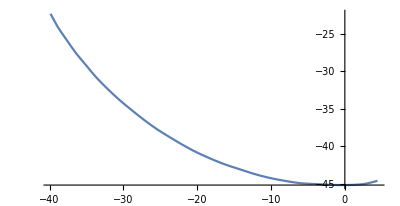

```mathematica
ParametricPlot[{xtape[t],ytape[t]},{t,t1,t2}]
```

```mathematica
dxtape[t_]=D[xtape[t],t]
```

InterpolatingFunction[…][t]

```mathematica
dytape[t_]=D[ytape[t],t]
```

InterpolatingFunction[…][t]

```mathematica
dstape[t_]=√(dxtape[t]^2+dytape[t]^2)
```

√((InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^2)

```mathematica
rtape[t_]=√(xtape[t]^2+ytape[t]^2)
```

√((InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^2)

```mathematica
omega[t_]=dstape[t]/rtape[t]
```

(√((InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^2))/(√((InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^2))

```mathematica
wave=1/(t2-t1)NIntegrate[omega[t],{t,t1,t2}]
```

2.7813

```mathematica
wave//Framed(*rad/s*)
```

2.7813